# Mathematica 图形图像语言及最新功能

## 陆玉柱, 资深软件工程师

## -Graphics--Graphics- #WolframTechConf

## 摘要

本次演讲主要概览简介Mathematica 图形图像语言及最新功能，包括：基于物理模型的光照渲染（MaterialShading），虚线的新功能，内置光线追踪（Ray tracing）及面向客户GLSL硬件渲染语言支持和客户自定义图形显示

## Mathematica 图形图像（Graphics）语言简介

Mathematica 图形图像（Graphics）语言是所有图形图像函数的基础, 所有图形图像函数都是通过Graphics语言来显示，交互，输出，打印...

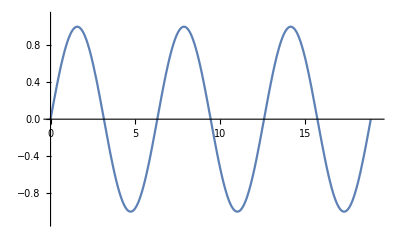

```mathematica
p=Plot[Sin[x],{x,0,6Pi}]
```

```mathematica
p//InputForm
```

### Graphics语言的构成: 元素（Primitives）/指令（Directives）/选项（Options）

#### 元素（Primitives）: Point/Line/Polygon/Sphere/Raster3D.... 指令（Directives）: Texture, RGBColor, FaceForm, EdgeForm, Thickness, Dashing... 选项（Options）: ImageSize, ViewPoint, AspectRatios.....

#### 二维：Graphics

```mathematica
Graphics[{FaceForm[Blue],EdgeForm[{Red,Thick,Dashed}],Polygon[{{0,0},{1,0},{0.5,1}},VertexColors->{Red, Green}],Disk[{2,2},.5]},Axes->True,PlotLabel->三角形与圆]
```

#### 三维：Graphics3D

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-1.99},{2,2,-1}]},Axes->True]
```

#### 自定义函数：

```mathematica
createCircle[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=With[{a=Det[({{x1, y1, 1}, {x2, y2, 1}, {x3, y3, 1}})],d=-Det[({{x1^2+y1^2, y1, 1}, {x2^2+y2^2, y2, 1}, {x3^2+y3^2, y3, 1}})],e=Det[({{x1^2+y1^2, x1, 1}, {x2^2+y2^2, x2, 1}, {x3^2+y3^2, x3, 1}})],f=-Det[({{x1^2+y1^2, x1, y1}, {x2^2+y2^2, x2, y2}, {x3^2+y3^2, x3, y3}})]},Circle[{-d/(2 a),-e/(2 a)},√((d^2+e^2)/(4 a^2)-f/a)]];
```

```mathematica
createCircle[pts_]:={};
DynamicModule[{pts={},c={}},ClickPane[Framed@Graphics[{Dynamic[c],Point[Dynamic[pts]]},PlotRange->5],(If[Length[pts]<3,AppendTo[pts,#],pts={#}];c=createCircle[pts])&]]
```

#### 碰撞模拟

```mathematica
Framed@DynamicModule[{contents={}},EventHandler[Graphics[{PointSize[0.1],Point[Dynamic[contents=Map[If[#[[1,2]]≥0,{#[[1]]-#[[2]],#[[2]]+{0,0.001}},{{#[[1,1]],0},{1,-0.8}#[[2]]}]&,contents];Map[First,contents]]]},PlotRange->{{0,1},{0,1}}],"MouseDown":>(AppendTo[contents,{MousePosition["Graphics"],{0,0}}])]]
```

## 带照明的立体渲染（Lighted Volume Rendering）

```mathematica
Graphics3D[{Specularity[White,30],Raster3D[RawArray["Byte",Import["ExampleData/CThead.tiff","Data"]],{{-1,-1,-1},{1,1,1}},{0,255},ColorFunction->#,Method->{ "VolumeLighting"->"EnhancedEdge","InterpolateValues"->True}]},ViewPoint->{-3.2,0.89,-0.34},ImageSize->300,Lighting->{{"Directional",White,ImageScaled[{0,0,2}]}}]&/@{(Blend[{{1,RGBColor[1.,1.,1.,0]},{0,RGBColor[0.,0.,0.,0.]},{0.35,RGBColor[0.33,0.33,0.33,0]},{0.66,RGBColor[0.66,0.66,0.66,0]},{0.21,RGBColor[0.19,0.19,0.19,0.34]},{0.19,RGBColor[0.17,0.17,0.17,0]},{0.27,RGBColor[0.25,0.25,0.25,0]}},#]&),(Blend[{{0, RGBColor[0.035,0.058,0,0]},{0.1, RGBColor[0.015,0,0.035,0]},{0.2, RGBColor[0,0,0,0.032]},{0.3, RGBColor[0.103,0.032,0,0]},{0.4, RGBColor[0,0,0,0]},{0.5, RGBColor[0.202,0.203,0.218,0.337]},{0.6, RGBColor[0.9,0.9,0.9,0.457]},{0.7, RGBColor[0.98,0.97,1,0.682]},{0.8, RGBColor[1,1,1,0.794]},{0.9, RGBColor[0.95,0.97,0.95,0.842]},{1, RGBColor[1,1,1,0.962]}}, #] &),(Blend[{{1,RGBColor[1., 1., 1., 1.]}, {0, RGBColor[0., 0., 0., 0]}, {0.32, RGBColor[0.5, 0.5, 0.5, 0.65]},{0.66,RGBColor[ 0.66, 0.66, 0.66, 0.66]}, {0.07,RGBColor[0.12, 0.12, 0.12, 0]}}, #]& )}
```

## 基于物理的渲染（MaterialShading）

MaterialShading是V12.3最新添加的渲染功能，是基于专业物理引擎PhysicsX开发的。

MaterialShadingpaclet:ref/MaterialShading["material"] 第一个参数可以设置预定义材质名称：

MaterialShadingpaclet:ref/MaterialShading[{"material",col}]   可以设置材质与颜色：

MaterialShadingpaclet:ref/MaterialShading[<|parm_1→val_1,…|>] 可以设置更为具体的各项参数，比如物理，表面，光源等参数

颜色类参数：

物理类参数：

几何参数：

表面参数：

anisotropy参数：

其他材质参数：

光照参数：

### 支持所有可视化函数

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},PlotPoints->80,PlotStyle->MaterialShading["Copper"],Mesh->None,Lighting->"ThreePoint"]
```

-Graphics-

```mathematica
Graphics3D[{MaterialShading["Gold"],ExampleData[{"Geometry3D","Beethoven"},"GraphicsComplex"]},Boxed-> False,Lighting->"ThreePoint"]
```

-Graphics3D-

```mathematica
Graphics3D[{MaterialShading[<|"BaseColor"-> Texture[-Graphics-],"SurfaceNormals"-> Texture[-Graphics-],"RoughnessCoefficient"-> 0.65,"MetallicCoefficient"-> Texture[-Graphics-] |>],Sphere[]},Lighting->"ThreePoint",Boxed->False,ViewPoint->Front]
```

-Graphics3D-

### 真实感绘制（Photorealistic shading）

```mathematica
(* Maps source: https://www.textures.com/download/PBR0950/140627 *)
Manipulate[
DynamicModule[{baseMap,normalMap,roughnessMap,metallicMap,emissionMap,aoMap},
{baseMap,normalMap,roughnessMap,metallicMap,emissionMap,aoMap}=Texture/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
Graphics3D[{MaterialShading[<|"BaseColor"->If[base,baseMap,Automatic],"SurfaceNormals"-> If[normal,normalMap,Automatic],"RoughnessCoefficient"-> If[roughness,roughnessMap,Automatic],"MetallicCoefficient"-> If[metallic,metallicMap,Automatic],"EmissionColor"-> If[emission,emissionMap,Automatic],"AmbientExposureFraction"-> If[ao,aoMap,Automatic],"TextureCoordinateScale"->2 {2,1}|>],Sphere[]},]
],
{{base,True,"Base Color"},{True,False}},
{{normal,True,"Normals"},{True,False}},
{{roughness,True,"Roughness"},{True,False}},
{{metallic,True,"Metallic"},{True,False}},
{{emission,True,"Emission"},{True,False}},
{{ao,True,"Ambient Occlusion"},{True,False}},
ControlPlacement->Left
]
```

### 更多细节请参考文档（Physically Based Rendering）

## 虚线的新功能

```mathematica
New Dashing Syntax: Dashing[r, offset, cap]
```

### 虚线偏移

```mathematica
Manipulate[Graphics[{Line[{{0,0},{2,1}}],AbsoluteDashing[{50,50},o],Red,Opacity[.5],Thickness[.01],Line[{{0,0},{2,1}}]}],{{o,0},-100,100}]
```

### 虚线偏移

```mathematica
Manipulate[Graphics[{Line[{{0,0},{2,1}}],Dashing[{.1,.1},0,CapForm[c]],Red,Opacity[.5],Thickness[.05],Line[{{0,0},{2,1}}]},PlotRange->{{-0.1,2.1},{-0.1,1.1}}],{c,{"Round","Butt","Square"}}]
```

```mathematica
Manipulate[Graphics[{Circle[],Dashing[{.1,.1},0,CapForm[c]],Red,Opacity[.5],Thickness[.05],Circle[]},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],{c,{"Round","Butt","Square"}}]
```

```mathematica
虚线偏移
```

### 也可应用于几何体的边界

```mathematica
Manipulate[Graphics[{EdgeForm[{Dashing[{.1,.1},o],Thickness[.01],Red}],Polygon[{{0,0},{2,1},{4,0}}]}],{{o,0},-0.1,0.1}]
```

```mathematica
Manipulate[Graphics[{EdgeForm[{Dashing[{.1,.1},o],Thickness[.01],Red}],Rectangle[]}],{{o,0},-0.1,0.1}]
```

```mathematica
Manipulate[Graphics[{EdgeForm[{Dashing[{.1,.1},o],Thickness[.01],Red}],Disk[]}],{{o,0},-0.1,0.1}]
```

### 应用例子

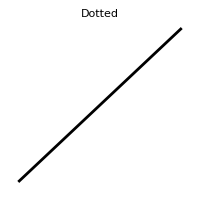
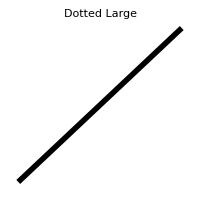
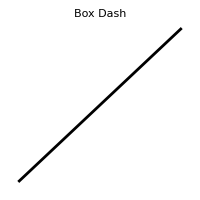
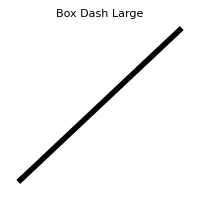
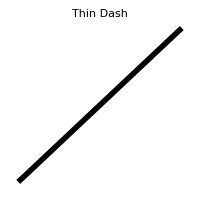
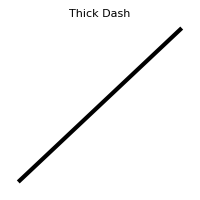
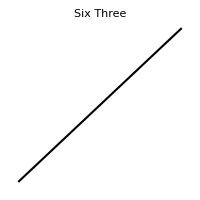
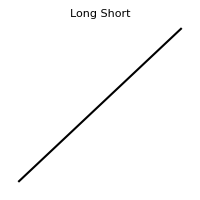
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
size=200;
Grid[{{Graphics[{AbsoluteDashing[{0,4},0,CapForm["Round"]],AbsoluteThickness[2],Line[{{0,0},{1,1}}]},PlotLabel->"Dotted",ImageSize->size],Graphics[{AbsoluteDashing[{0,8},0,CapForm["Round"]],AbsoluteThickness[4],Line[{{0,0},{1,1}}]},PlotLabel->"Dotted Large",ImageSize->size],Graphics[{AbsoluteDashing[{0,4},0,CapForm["Square"]],AbsoluteThickness[2],Line[{{0,0},{1,1}}]},PlotLabel->"Box Dash",ImageSize->size],Graphics[{AbsoluteDashing[{0,8},0,CapForm["Square"]],AbsoluteThickness[4],Line[{{0,0},{1,1}}]},PlotLabel->"Box Dash Large",ImageSize->size],Graphics[{AbsoluteDashing[{1,2},0,CapForm["Butt"]],AbsoluteThickness[4],Line[{{0,0},{1,1}}]},PlotLabel->"Thin Dash",ImageSize->size],Graphics[{AbsoluteDashing[{4,1},0,CapForm["Butt"]],AbsoluteThickness[3],Line[{{0,0},{1,1}}]},PlotLabel->"Thick Dash",ImageSize->size]},{Graphics[{AbsoluteDashing[{6,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}}]},PlotLabel->"Six Three",ImageSize->size],Graphics[{AbsoluteDashing[{18,3,6,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}}]},PlotLabel->"Long Short",ImageSize->size],Graphics[{AbsoluteDashing[{18,3,6,3,6,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}}]},PlotLabel->"Long Short Short",ImageSize->size],Graphics[{AbsoluteDashing[{18,3,6,3,6,3,6,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}}]},PlotLabel->"Long Short Short Short",ImageSize->size],Graphics[{AbsoluteDashing[{18,3,1,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}}]},PlotLabel->"Long Dot",ImageSize->size],Graphics[{AbsoluteDashing[{18,3,1,3,1,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}}]},PlotLabel->"Long Dot Dot",ImageSize->size]},{Graphics[{AbsoluteDashing[{18,3,1,3,1,3,1,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}}]},PlotLabel->"Long Dot Dot Dot",ImageSize->size],Graphics[{AbsoluteThickness[1],Line[{{0,0},{1,1}}],AbsoluteDashing[{.5,18},0,CapForm["Butt"]],AbsoluteThickness[8],Line[{{0,0},{1,1}}]},PlotLabel->"Railroad",ImageSize->size],
Graphics[{AbsoluteThickness[3],CapForm["Butt"],Line[{{0,0},{1,1}}],AbsoluteDashing[{9},0,CapForm["Butt"]],AbsoluteThickness[2.5],White,Line[{{0,0},{1,1}}]},PlotLabel->"Black White Dash",ImageSize->size],
Graphics[{AbsoluteDashing[{8,3},0,CapForm["Butt"]],AbsoluteThickness[3.5],Line[{{0,0},{1,1}}],AbsoluteThickness[2.5],CapForm["Square"],White,Line[{{0,0},{1,1}}]},PlotLabel->"Double Dash",ImageSize->size],Graphics[{AbsoluteDashing[{8,8},0,CapForm["Round"]],AbsoluteThickness[4],Line[{{0,0},{1,1}}]},PlotLabel->"Dash Rounded",ImageSize->size]},{Graphics[{AbsoluteThickness[1.5],CapForm["Butt"],GrayLevel[.5],Line[{{0,0},{1,1}}],AbsoluteDashing[{6},0,CapForm["Butt"]],AbsoluteThickness[1.5],Black,Line[{{0,0},{1,1}}]},PlotLabel->"Black Gray Dash",ImageSize->size],
Graphics[{AbsoluteThickness[1],CapForm["Butt"],Line[{{0,0},{1,1}}],AbsoluteDashing[{0,15},0,CapForm["Round"]],AbsoluteThickness[5],Line[{{0,0},{1,1}}]},PlotLabel->"Line Dot",ImageSize->size],Graphics[{AbsoluteThickness[1],CapForm["Butt"],Line[{{0,0},{1,1}}],AbsoluteDashing[{0,15},0,CapForm["Square"]],AbsoluteThickness[4],Line[{{0,0},{1,1}}]},PlotLabel->"Line Box",ImageSize->size],Graphics[{AbsoluteDashing[{16,1,8,2,4,3,2,4,1,5},0,CapForm["Butt"]],AbsoluteThickness[2],Black,Line[{{0,0},{1,1}}]},PlotLabel->"Log Line",ImageSize->size],Graphics[{AbsoluteDashing[{20,4},0,CapForm["Round"]],AbsoluteThickness[3],GrayLevel[.8],Line[{{0,0},{1,1}}],AbsoluteDashing[{14,10},0,CapForm["Round"]],AbsoluteThickness[2],GrayLevel[.6],Line[{{.01,.01},{1,1}}],AbsoluteDashing[{6,18},0,CapForm["Round"]],AbsoluteThickness[1],GrayLevel[0],Line[{{.025,.025},{1,1}}]},PlotLabel->"Blurred Dash",ImageSize->size]}}]
```

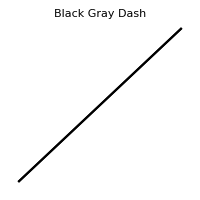
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
size=200;
Grid[{{Graphics[{AbsoluteDashing[{0,4},0,CapForm["Round"]],AbsoluteThickness[2],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Dotted",ImageSize->size],Graphics[{AbsoluteDashing[{0,8},0,CapForm["Round"]],AbsoluteThickness[4],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Dotted Large",ImageSize->size],Graphics[{AbsoluteDashing[{0,4},0,CapForm["Square"]],AbsoluteThickness[2],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Box Dash",ImageSize->size],Graphics[{AbsoluteDashing[{0,8},0,CapForm["Square"]],AbsoluteThickness[4],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Box Dash Large",ImageSize->size],Graphics[{AbsoluteDashing[{1,2},0,CapForm["Butt"]],AbsoluteThickness[4],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Thin Dash",ImageSize->size],Graphics[{AbsoluteDashing[{4,1},0,CapForm["Butt"]],AbsoluteThickness[3],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Thick Dash",ImageSize->size]},{Graphics[{AbsoluteDashing[{6,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Six Three",ImageSize->size],Graphics[{AbsoluteDashing[{18,3,6,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Long Short",ImageSize->size],Graphics[{AbsoluteDashing[{18,3,6,3,6,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Long Short Short",ImageSize->size],Graphics[{AbsoluteDashing[{18,3,6,3,6,3,6,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Long Short Short Short",ImageSize->size],Graphics[{AbsoluteDashing[{18,3,1,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Long Dot",ImageSize->size],Graphics[{AbsoluteDashing[{18,3,1,3,1,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Long Dot Dot",ImageSize->size]},{Graphics[{AbsoluteDashing[{18,3,1,3,1,3,1,3},0,CapForm["Butt"]],AbsoluteThickness[1.5],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Long Dot Dot Dot",ImageSize->size],Graphics[{AbsoluteThickness[1],Line[{{0,0},{1,1}},VertexColors->{Red, Green}],AbsoluteDashing[{.5,18},0,CapForm["Butt"]],AbsoluteThickness[8],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Railroad",ImageSize->size],
Graphics[{AbsoluteThickness[3],CapForm["Butt"],Line[{{0,0},{1,1}},VertexColors->{Red, Green}],AbsoluteDashing[{9},0,CapForm["Butt"]],AbsoluteThickness[2.5],White,Line[{{0,0},{1,1}}]},PlotLabel->"Black White Dash",ImageSize->size],
Graphics[{AbsoluteDashing[{8,3},0,CapForm["Butt"]],AbsoluteThickness[3.5],Line[{{0,0},{1,1}},VertexColors->{Red, Green}],AbsoluteThickness[2.5],CapForm["Square"],White,Line[{{0,0},{1,1}}]},PlotLabel->"Double Dash",ImageSize->size],Graphics[{AbsoluteDashing[{8,8},0,CapForm["Round"]],AbsoluteThickness[4],Line[{{0,0},{1,1}},VertexColors->{Red, Green}]},PlotLabel->"Dash Rounded",ImageSize->size]},{Graphics[{AbsoluteThickness[1.5],CapForm["Butt"],Line[{{0,0},{1,1}},VertexColors->{{1,0,0,0.5},{0,1,0,0.5}}],AbsoluteDashing[{6},0,CapForm["Butt"]],AbsoluteThickness[1.5],Opacity[1],Line[{{0,0},{1,1}},VertexColors->{Red,Green}]},PlotLabel->"Black Gray Dash",ImageSize->size],
Graphics[{AbsoluteThickness[1],CapForm["Butt"],Line[{{0,0},{1,1}},VertexColors->{Red,Green}],AbsoluteDashing[{0,15},0,CapForm["Round"]],AbsoluteThickness[5],Line[{{0,0},{1,1}},VertexColors->{Red,Green}]},PlotLabel->"Line Dot",ImageSize->size],Graphics[{AbsoluteThickness[1],CapForm["Butt"],Line[{{0,0},{1,1}},VertexColors->{Red,Green}],AbsoluteDashing[{0,15},0,CapForm["Square"]],AbsoluteThickness[4],Line[{{0,0},{1,1}},VertexColors->{Red,Green}]},PlotLabel->"Line Box",ImageSize->size],Graphics[{AbsoluteDashing[{16,1,8,2,4,3,2,4,1,5},0,CapForm["Butt"]],AbsoluteThickness[2],Black,Line[{{0,0},{1,1}},VertexColors->{Red,Green}]},PlotLabel->"Log Line",ImageSize->size],Graphics[{AbsoluteDashing[{20,4},0,CapForm["Round"]],AbsoluteThickness[3],GrayLevel[.8],Line[{{0,0},{1,1}},VertexColors->{RGBColor[1,0,0,0.5],RGBColor[0,1,0,0.5]}],AbsoluteDashing[{14,10},0,CapForm["Round"]],AbsoluteThickness[2],GrayLevel[.6],Line[{{.01,.01},{1,1}},VertexColors->{RGBColor[1,0,0,0.75],RGBColor[0,1,0,0.75]}],AbsoluteDashing[{6,18},0,CapForm["Round"]],AbsoluteThickness[1],GrayLevel[0],Line[{{.025,.025},{1,1}},VertexColors->{RGBColor[1,0,0],RGBColor[0,1,0]}]},PlotLabel->"Blurred Dash",ImageSize->size]}}]
```

```mathematica
size=200;
Grid[{{Graphics3D[{AbsoluteDashing[{0,4},0,CapForm["Round"]],AbsoluteThickness[2],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Dotted",ImageSize->size],Graphics3D[{AbsoluteDashing[{0,8},0,CapForm["Round"]],AbsoluteThickness[4],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Dotted Large",ImageSize->size],Graphics3D[{AbsoluteDashing[{0,4},0,CapForm["Square"]],AbsoluteThickness[2],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Box Dash",ImageSize->size],Graphics3D[{AbsoluteDashing[{0,8},0,CapForm["Square"]],AbsoluteThickness[4],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Box Dash Large",ImageSize->size],Graphics3D[{AbsoluteDashing[{1,2}],AbsoluteThickness[4],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Thin Dash",ImageSize->size],Graphics3D[{AbsoluteDashing[{4,1}],AbsoluteThickness[3],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Thick Dash",ImageSize->size]},{Graphics3D[{AbsoluteDashing[{6,3}],AbsoluteThickness[1],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Six Three",ImageSize->size],Graphics3D[{AbsoluteDashing[{18,3,6,3}],AbsoluteThickness[1],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Long Short",ImageSize->size],Graphics3D[{AbsoluteDashing[{18,3,6,3,6,3}],AbsoluteThickness[1],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Long Short Short",ImageSize->size],Graphics3D[{AbsoluteDashing[{18,3,6,3,6,3,6,3}],AbsoluteThickness[1],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Long Short Short Short",ImageSize->size],Graphics3D[{AbsoluteDashing[{18,3,1,3}],AbsoluteThickness[1],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Long Dot",ImageSize->size],Graphics3D[{AbsoluteDashing[{18,3,1,3,1,3}],AbsoluteThickness[1],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Long Dot Dot",ImageSize->size]},{Graphics3D[{AbsoluteDashing[{18,3,1,3,1,3,1,3}],AbsoluteThickness[1],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Long Dot Dot Dot",ImageSize->size],Graphics3D[{AbsoluteThickness[.5],Line[{{0,0,0},{1,1,1}}],AbsoluteDashing[{.5,18}],AbsoluteThickness[8],CapForm["Butt"],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Railroad",ImageSize->size],
Graphics3D[{AbsoluteThickness[3],CapForm["Butt"],Line[{{0,0,0},{1,1,1}}],AbsoluteDashing[{9}],AbsoluteThickness[2.5],CapForm["Butt"],White,Line[{{0,0,0},{1,1,1.001}}]},PlotLabel->"Black White Dash",ImageSize->size],
Graphics3D[{AbsoluteDashing[{8,3}],AbsoluteThickness[3],CapForm["Butt"],Line[{{0,0,0},{1,1,1}}],AbsoluteThickness[2.5],CapForm["Square"],White,Line[{{0,0,0},{1,1,1.001}}]},PlotLabel->"Double Dash",ImageSize->size],Graphics3D[{AbsoluteDashing[{8,8}],AbsoluteThickness[4],CapForm["Round"],Line[{{0,0,0},{1,1,1}}]},PlotLabel->"Dash Rounded",ImageSize->size]}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- |

## 内置光线追踪（Ray tracing）

Mac平台V12.2，开始测试新的Ray tracing功能

### 新光源（“Area”）

```mathematica
RayTrace[expr_]:=Style[expr,RenderingOptions->{"3DRenderingMethod"->"RayTracing"}];
lpos={2,-2,7};lcol=White;
RayTrace[Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-1.99},{2,2,-1}]},ImageSize->{400,400},Lighting->#]]&/@{{{"Area",lcol,lpos,{{1,0.0,0},{0,0.5,0}}}},Automatic}
```

-Graphics-

### “RayTracing” 参数

```mathematica
wall1=Polygon[{{-1,0,1.3},{-1,0,-1},{-1,2.0,-1},{-1,2.0,1.3}}];
wall2=Polygon[{{1,0,1.3},{1,2.0,1.3},{1,2.0,-1},{1,0,-1}}];
floor=Polygon[{{-1,0,1.3},{1,0,1.3},{1,0,-1},{-1,0,-1}}];
backWall=Polygon[{{-1,0,-1},{1,0,-1},{1,2,-1},{-1,2,-1}}];
floorCenter={-0.5,0,-0.5};
Tl=TranslationTransform[floorCenter+{-0.55,0.0,-0.483}];
Rl=RotationTransform[0.5,{0,1,0}];
Sl=ScalingTransform[{0.6,1.2,0.6}];
largeTransform=Composition[Sl,Rl,Tl];
largeBox=GeometricTransformation[Cuboid[],largeTransform];

Ts=TranslationTransform[floorCenter+{0.85,0.0,0.55}];
Rs=RotationTransform[-0.4,{0.0,1.0,0.0}];
Ss=ScalingTransform[{0.6,0.6,0.6}];
smallTransform=Composition[Ss,Rs,Ts];
```

```mathematica
Graphics3D[{Blue,Ball[{0.35,0.4,0.55},0.4],Red,wall1,Green,wall2,LightGray,floor,backWall,largeBox },ImageSize->{400,400},ViewPoint->{0,0,3},ViewVertical->{0,1,0},Lighting->{{"Area",White,{0,1.9,0},{{0.45,0.0,0},{0,0,0.3}}}}]
```

-Graphics3D-

```mathematica
RayTrace[Graphics3D[{Blue,Ball[{0.35,0.4,0.55},0.4],Red,wall1,Green,wall2,LightGray,floor,backWall,largeBox },ImageSize->{400,400},SphericalRegion->False,ViewPoint->{0,0,3},ViewVertical->{0,1,0},Lighting->{{"Area",White,{0,1.9,0},{{0.45,0.0,0},{0,0,0.3}}}},Method->{"RayTracing"->{"ImageSamples"->40,"RayBounces"->#}}]]&/@{1,2,3,4}
```

-Graphics-

```mathematica
RayTrace[Graphics3D[{Blue,Ball[{0.35,0.4,0.55},0.4],Red,wall1,Green,wall2,LightGray,floor,backWall,largeBox },ImageSize->{400,400},SphericalRegion->False,ViewPoint->{0,0,3},ViewVertical->{0,1,0},Lighting->{{"Area",White,{0,1.9,0},{{0.45,0.0,0},{0,0,0.3}}}},Method->{"RayTracing"->{"ImageSamples"->#,"RayBounces"->3}}]]&/@{10,20,30,40}
```

-Graphics-

## GLSL硬件渲染语言支持和客户自定义图形显示

从V12.2开始，添加了新的GLSL硬件渲染功能

A simple example to try some online shader from: https://doc.qt.io/qt-5.9/qtopengl-cube-vshader-glsl.html

```mathematica
shader2=<|
"Name"->"Cube",
"Attributes"-><|"a_position"->"ATTRIB_VERTEX","a_texcoord"->"ATTRIB_TEXTURECOORD"|>,"Parameters"-><|"Matrix"->{"mvp_matrix","TRANSFORMMATRIX","MATRIX4"}|>,"ShaderPrograms"-><|"GLFragmentProgram"->"fShader.glsl","GLVertexProgram"->"vShader.glsl"|>
|>;
```

```mathematica
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@shader2];
```

```mathematica
Graphics[{SurfaceAppearance["Cube"],Texture[-Graphics-],Polygon[{{0,0},{1,0},{1/2,1}},VertexTextureCoordinates->{{0,0},{1,0},{1/2,1}}]}]
```

### 利用已有的GLSL资源

A list of algorithm art from: http://algorithmicartmeetup.blogspot.com/2017/04/accelerated-art-with-glsl.html

```mathematica
{s1,s2,s3,s4,s5,s6}=<|
"Name"->#,
"Attributes"-><|"a_position"->"ATTRIB_VERTEX","a_texcoord"->"ATTRIB_TEXTURECOORD"|>,"Parameters"-><|"Matrix"->{"mvp_matrix","TRANSFORMMATRIX","MATRIX4"},"Time"->{"time",0,"NUMBER"},"Resolution"->{"resolution", {200,200},"NUMBER2"}|>,"ShaderPrograms"-><|"GLFragmentProgram"->#,"GLVertexProgram"->"vShader.glsl"|>
|>&/@{"fShader1.glsl","fShader2.glsl","fShader3.glsl","fShader4.glsl","fShader5.glsl","fShader6.glsl"};
```

```mathematica
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@s1];
Manipulate[Graphics[{SurfaceAppearance["fShader1.glsl","Time"->Dynamic@time],Rectangle[]},ImageSize->{400,400}],{time,0,100}]
```

```mathematica
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@s2];
Manipulate[Graphics[{SurfaceAppearance["fShader2.glsl","Time"->Dynamic@time],Rectangle[]},ImageSize->{400,400}],{time,0,10}]
```

```mathematica
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@s3];
Manipulate[Graphics[{SurfaceAppearance["fShader3.glsl","Time"->Dynamic@time],Rectangle[]},ImageSize->{400,400}],{time,0,10}]
```

```mathematica
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@s4];
Manipulate[Graphics[{SurfaceAppearance["fShader4.glsl","Time"->Dynamic@time],Rectangle[]},ImageSize->{400,400}],{time,0,10}]
```

```mathematica
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@s5];
Manipulate[Graphics[{SurfaceAppearance["fShader5.glsl","Time"->Dynamic@time],Rectangle[]},ImageSize->{400,400}],{time,0,10}]
```

```mathematica
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@s6];
Manipulate[Graphics[{SurfaceAppearance["fShader6.glsl","Time"->Dynamic@time],Rectangle[]},ImageSize->{400,400}],{time,0,1}]
```

### 移植其他 Shader Projects

Another example from users kode life project: https://hexler.net/products/kodelife to to mimic the old iTunes Jelly shader:

```mathematica
KodeLifeA=<|
"Name"->"KodeLifeA",
"Attributes"-><|"a_position"->"ATTRIB_VERTEX","a_texcoord"->"ATTRIB_TEXTURECOORD"|>,"Parameters"-><|"Matrix"->{"mvp","TRANSFORMMATRIX","MATRIX4"},"Time"->{"time",0,"NUMBER"},"Spectrum"->{"spectrum", {0,1,0},"NUMBER3"}|>,"ShaderPrograms"-><|"GLFragmentProgram"->"fShaderKodeLifeA.glsl","GLVertexProgram"->"vShaderKodeLifeA.glsl"|>
|>;
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@KodeLifeA];
```

```mathematica
Manipulate[Graphics[{SurfaceAppearance["KodeLifeA","Time"->Dynamic@time,Texture[{{0,0}}]],Rectangle[]},ImageSize->{300,300}],{time,0,100}]
```

Multiple pass through Texture:

```mathematica
KodeLifeB=<|
"Name"->"KodeLifeB",
"Attributes"-><|"a_position"->"ATTRIB_VERTEX","a_texcoord"->"ATTRIB_TEXTURECOORD"|>,
"Parameters"-><|"Matrix"->{"mvp","TRANSFORMMATRIX","MATRIX4"},"Resolution"->{"resolution", {1,1},"NUMBER2"}|>,"ShaderPrograms"-><|"GLFragmentProgram"->"fShaderKodeLifeB.glsl","GLVertexProgram"->"vShaderKodeLifeA.glsl"|>
|>;
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@KodeLifeB];
```

```mathematica
Manipulate[With[{t=time},Graphics[{SurfaceAppearance["KodeLifeB",Texture@Graphics[{SurfaceAppearance["KodeLifeA","Time"->Dynamic@t,Texture[{{0,0}}]],Rectangle[]},ImageSize->{300,300}]],Rectangle[]},ImageSize->{300,300}]],{time,0,100}]
```

```mathematica
Animate[With[{t=time},Graphics[{SurfaceAppearance["KodeLifeB",Texture@Graphics[{SurfaceAppearance["KodeLifeA","Time"->Dynamic@t,Texture[{{0,0}}]],Rectangle[]},ImageSize->{300,300}]],Rectangle[]},ImageSize->{300,300}]],{time,0,10}]
```

### 自定义可视化函数: Move Computing from CPU to GPU (No data traffic, No CPU cost)

```mathematica
Import["fShaderTemplate.glsl"]
```

const float tau = 3.14159;

uniform float time;
uniform vec2 resolution;

void main(void) {
  vec2 uv = (2.0 * gl_FragCoord.xy - resolution) / min(resolution.x, resolution.y) * tau;
  float x = uv.x;
  float y = uv.y;
  float v = customizedFunc;
  v *= 0.125;
  v += (time * 0.1);
  vec3 c = vec3(0.5) + 0.9 * cos(2 * tau * (v + vec3(0.2, 0.4, 0.8)));
  gl_FragColor = vec4(vec3(c), 1.0);
}

```mathematica
compileNewGLSLPlot[s_]:=StringReplace[#,"customizedFunc"->s]&;
```

```mathematica
MyFancyGPUDensityPlot[s_]:=With[{ss=compileNewGLSLPlot[s][Import["fShaderTemplate.glsl"]]},
Export["fShaderCustomize.glsl",ss,"TEXT"];shaderList ="fShaderCustomize.glsl";
s1=<|
"Name"->shaderList,
"Attributes"-><|"a_position"->"ATTRIB_VERTEX","a_texcoord"->"ATTRIB_TEXTURECOORD"|>,"Parameters"-><|"Matrix"->{"mvp_matrix","TRANSFORMMATRIX","MATRIX4"},"Time"->{"time",0,"NUMBER"},"Resolution"->{"resolution", {200,200},"NUMBER2"}|>,"ShaderPrograms"-><|"GLFragmentProgram"->shaderList,"GLVertexProgram"->"vShader.glsl"|>
|>;
FE`Evaluate@Evaluate[FEPrivate`AddSurfaceAppearanceDefinition@#]&/@{s1};
Manipulate[Graphics[{SurfaceAppearance[shaderList,"Time"->Dynamic@time],Rectangle[]},ImageSize->{350,350}],{time,0,10}]]
```

```mathematica
MyFancyGPUDensityPlot["sin(x*y)"]
```

## 资源链接

[文档中心（Documentation）](https://reference.wolfram.com/language/index.html.zh?source=footer)

[项目演示（Demonstration）](https://demonstrations.wolfram.com)